```mathematica
Clear["Global`*"];
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
(*myDir="C:\\Mathematica Works";
SetDirectory[myDir];
errTol=10^-6//N;

Get["InteriorPointMethod`"];
Get["Cplex4Mathematica`"];
Get["Cplex4MathematicaMIQP`"];
Get["ParametricPolyApp`"];
(*Get["SQPMathematica`"];*)

(*install cplex*)
Get["NETLink`"];

UninstallNET[];
InstallNET[];
pathConcert="D:\\IBM\\ILOG\\CPLEX_Studio126\\cplex\\bin\\x64_win64\\ILOG.Concert.dll";
pathCPLEX="D:\\IBM\\ILOG\\CPLEX_Studio126\\cplex\\bin\\x64_win64\\ILOG.CPLEX.dll";
LoadNETAssembly[pathConcert];
LoadNETAssembly[pathCPLEX];*)
```

```mathematica
(************************************function formulation*************************************)
CapaPriceDistributionProgram[flagCapa_,CapaGivenVal_,horizonDispatch_,periodDispatch_(*,priceInner_,priceH2Inner_*)(*,pricePurch_*),IRRLower_,IRRUpper_,nDiscret_,boundarypriceInner_,boundarypriceH2Inner_,itrdays_,flagGrid_,ExchangeRate_,periodTOU_,flagTOUH_,TOUHYear_,priceFITGVal_,flagTOUHPurch_,TOUHYearPurch_,pricePurchGVal_,priceNH3_,ratepAEMin_,LoadNH3Min_,rateDiscount_,flagOverShootLimit_,RateTimeOverShoot_,coeffPunish_,flagMMA_,ConstCapacityMonth_,flagConnected_,flagBatExist_,flagPlace_, (*WTS_,flagWTS_,Gridratio_,flagGridratio_,*)buffer_,flagbuffer_, EL_, flagEL_, constG2L_, ETotal_, yitaP2H_]:=Module[{},

(****************************** System Modeling ******************************)
(*Battery/Li*)
capacityBattery=0.1;
PbatMax=1000;(*35MW*)
PbatMin=-0.1;(*35MW*)
EbatMax=0.1;(*35MWh*)
SOCiniVal=0.5;
SOCMin=0.1;
SOCMax=0.9;
varsCtrlBat={PbatCh,PbatDisc};
varsStateBat={ESOC};
boolsBatA={boolsBat};
equStateBat={};
alphaBat=0.5*10^-2/24/3600;
betaBatCh=0.95;
betaBatDisc=1/0.95;
varsCapaBatA={varsCapaBat};
MaxPbatA={MaxPbat};
AppendTo[equStateBat,-alphaBat*ESOC-(betaBatDisc PbatDisc-betaBatCh PbatCh)/3600//N];

(*(*No Battery in this research*)
varsCtrlBat={};
varsStateBat={};
equStateBat={};*)


(*Alkaline electrolyzer*)
varsCtrlAE={pAE,pAEInner,pAEPurch};
yitaH2=yitaP2H;(*5kwh/Nm3*)
equAE=yitaH2* qH2In*10^(-3)//N;
varsCapaAEA={varsCapaAE};

(*Hydrogen Buffer Tank*)
varsnStoMaxA={varsnStoMax};
varsStateSto={nSto};(*Nm3*)
varsCtrlSto={qH2In,qH2Out};(*Nm3/h*)
equStateSto={};
AppendTo[equStateSto,(qH2In-qH2Out)/3600//N];
varsCapaHSA={varsCapaHS};

(*obtain N2 from the air/Pressure Swing Adsorption(PSA)*)
varsCtrlPSA={pPSA};
equPSA={0*qH2Out};
(*equPSA={1.064*10^(-4)*qH2Out};*)

(*Synthetic Ammonia/Haber-Bosch synthesis(HBS)*)
varsCtrlHBS={pHBS};
equHBS={2.9*10^(-4)*qH2Out};
(*equHBS={0.5*4.316*10^(-4)*qH2Out};*)
ConstMWh2t=2/3*200*1000/22.4*17*10^-6//N;

varsCtrlSA={pSA,pSAInner,pSAPurch};

(*Slow Dynamics*)
varsStateA=Join[varsStateSto,If[flagBatExist,varsStateBat,{}]];
varsCtrlA=Join[varsCtrlSto,varsCtrlAE,varsCtrlPSA,varsCtrlHBS,varsCtrlSA,If[flagBatExist,varsCtrlBat,{}]];
equStateA=Join[equStateSto,If[flagBatExist,equStateBat,{}]];
(*varsStateA=Join[varsStateBat,varsStateSto];
varsCtrlA=Join[varsCtrlBat,varsCtrlSto,varsCtrlAE,varsCtrlPSA,varsCtrlHBS];
equStateA=Join[equStateBat,equStateSto];
*)

pwA={pw1};
pvA={pv1};
pwCurtA={pwCurt};
pwCurtA={pwCurt};
pPurchA={pPurch};
(*boolsCurtA={boolsCurt};
boolsPurchA={boolsPurch};*)
boolsExchangeA={boolsExchange};
varsCapaRenA={varsCapaWind,varsCapaSolar};
(*Capacity variables*)
varsCapaA=Join[varsCapaRenA,varsCapaAEA,varsCapaHSA,varsCapaBatA,MaxPbatA];

flagNormData=False;(*True-normal data;False-real data in Gansu*)

(*choose wind+pv data*)

(*If[flagPlace==2,*)
(*Neimeng real data*)
(*PV generation*)
periodSolar=3600;
tmp=Import["C:\\Users\\LJR\\Desktop\\code\\code\\core\\RE.xlsx",{"Data",flagPlace,1;;8760,2;;2}]//Transpose//Flatten;
(*(*betaSolar=0.608;*)(*)*0.24-1675.85h; 0.312-1700h; 0.608-1800h*)*)
psolarToNorm=tmp;(*Table[Min[tmp[[i]](1-betaSolar tmp[[i]](tmp[[i]]-1)),1],{i,1,Length[tmp]}];*)
Print["Max generation of Wind power is: ",Max[psolarToNorm]," p.u."];
AUHS=Total[psolarToNorm]/1/(3600/periodSolar);
Print["Annual ultilization hours of pv is: ",AUHS," h"];
(*wind generation*)
periodWind=3600;
tmp=Import["C:\\Users\\LJR\\Desktop\\code\\code\\core\\RE.xlsx",{"Data",flagPlace,1;;8760,1;;1}]//Transpose//Flatten;
(*betaWind=0.7625;*)(*0.361-3300h; 0.7625-3500h; 0.8221-3625h*)
pwindToNorm=tmp;(*Table[Min[tmp[[i]](1-betaWind tmp[[i]](tmp[[i]]-1)),1],{i,1,Length[tmp]}];*)
Print["Max generation of PV is: ",Max[pwindToNorm]," p.u."];
AUHW=Total[pwindToNorm]/1/(3600/periodWind);
Print["Annual ultilization hours of Wind power is: ",AUHW," h"];
(*];*)

(****************************** Year ahead Dispatch ******************************)
(*periodDispatch=1*4*900 ; (*time interval, typically be 1h*)*)
periodNH3Dispatch=itrdays(**24*)*3600;(*period of Synthetic Ammonia, typically be 1 day*)
(*horizonDispatch=365*24*3600;*)
horizonAll=horizonDispatch;
Tothours=horizonDispatch/3600;
nDispatch=horizonDispatch/periodDispatch;
Ttrans=2*3600;(*Time Constant of Synthetic Ammonia is 2h/4h*)
nAll=horizonAll/periodDispatch;

(*wind and solar power process*)
ftmp[i_]:=Module[{},Mean[psolarToNorm[[#]]&/@Range[i periodDispatch/periodSolar+1,(i+1) periodDispatch/periodSolar,1]]];
pvNormMeanValAll=Parallelize[Map[ftmp,Range[0,nAll-1]]];
pvNormMeanValAll=Table[If[pvNormMeanValAll[[i]]<0,0,pvNormMeanValAll[[i]]],{i,1,pvNormMeanValAll//Length}];
pwNormMeanValAll=Table[Mean[pwindToNorm[[#]]&/@Range[i periodDispatch/periodWind+1,(i+1)periodDispatch/periodWind,1]],{i,0,nAll-1}];
TOUHYearMeanValAll=If[flagTOUH,Table[Mean[TOUHYear[[#]]&/@Range[i periodDispatch/periodTOU+1,(i+1)periodDispatch/periodTOU,1]],{i,0,nAll-1}],Table[priceFITGVal,{i,0,nAll-1}]];
TOUHYearPurchMeanValAll=If[flagTOUHPurch,Table[Mean[TOUHYearPurch[[#]]&/@Range[i periodDispatch/periodTOU+1,(i+1)periodDispatch/periodTOU,1]],{i,0,nAll-1}],Table[pricePurchGVal,{i,0,nAll-1}]];
(******************** Controller Objective Function and Limits ********************)
InfDef=10^9;
(*weight of multi-agents*)
weightRen=1;
weightAEHS=1;
weightSA=1;

(*Capacity Given*)

varsCapaWindGVal=CapaGivenVal[[1]];(*200*)
varsCapaSolarGVal=CapaGivenVal[[2]];(*200*)
varsCapaAEGVal=CapaGivenVal[[3]];(*100*)
varsCapaHSGVal=CapaGivenVal[[4]];(*10^5*)
varsCapaBatGVal=CapaGivenVal[[5]];(*MWh*)
varsCapaBatEnergyGVal=varsCapaBatGVal[[1]];
varsCapaBatPowerGVal=varsCapaBatGVal[[2]];
(*varsWTS=WTS;
varsGridratio=Gridratio;*)
varsbuffer=buffer;
varsEL=EL;
(*parameter of price: ep-￥/MWh; H2-￥/Nm3; NH3-￥/t*)
(*priceFIT=0.2829*10^3;(*feed-in-tariff*)*)
(*pricePurch=0.42*10^3;(*electricity price*)*)
(*priceNH3=3060;*)

priceInnerA={priceInner};
priceH2InnerA={priceH2Inner};
priceFITA={priceFIT};
pricePurchA={pricePurch};
(*priceInner=0.178*10^3;
priceH2Inner=1.27;*)

(*signal*)
flagRenCapa=flagCapa[[1]];(*True-optimal; False-given*)
flagWindCapa=flagRenCapa[[1]];
flagSolarCapa=flagRenCapa[[2]];
flagAECapa=flagCapa[[2]];(*True-optimal; False-given*)
flagHSCapa=flagCapa[[3]];(*True-optimal; False-given*)
flagBatCapa=flagCapa[[4]];(*True-optimal; False-given*)
flagBatCapaEnergy=flagBatCapa[[1]];
flagBatCapaPower=flagBatCapa[[2]];
(*FlagWTS=flagWTS;
FlagGridratio=flagGridratio;*)
Flagbuffer=flagbuffer;
FlagEL=flagEL;
(*Operation parameters*)
(*Alkaline Electrolyzor*)
(*ratepAEMin=0.05;(*considering Unit Commitment of AEs; single-0.2;UC-0.05;*)*)
RateOverShoot=0.0;(*overshoot rate of AE*)
(*Hydrogen Storage/buffer tank*)
yitaMin=0.1;
yitaMax=0.9;

(*Synthetic Ammonia*)
(*LoadNH3Min=0.3;*)
LimitRampingNH3=0.5;
(*itrdays=1;(*1 day*)*)

(*exchange to grid: net*)
(*ExchangeRate=0.2;*)

(*Economic parameters*)
(*rateDiscount=0.06;*)
OperationYearsRen=20;
OperationYearsAEHS=15;
OperationYearsSA=20;
(*Investment: W￥/MW or W￥/Nm3*)
ISInit=400;
ISOM=ISInit*0.02;
IWInit=600;
IWOM=IWInit*0.02;
IAEInit=300;
IAEOM=IAEInit*0.03;
IHSInit=500*10^-4;
IHSOM=IHSInit*0.02;
ISAInit=2.6*10^4;
ISAOM=0.03 ISAInit;
IBatInit=180;(*W￥/MWh*)
IBatOM=0.01IBatInit;
(*ISAInit=260;
ISAOM=ISAInit*0.02;*)

ConstG2L=constG2L;(*4.84*10^-4//N;*)(*nH2 To mNH3; t/Nm3*)
ConstG2LH2=1000/22.4*2*10^-6//N;(*nH2 To mH2; t/Nm3*)
(*ConstCapacityMonth=33*10^3/10^4;(*容量费按照最大需量-可优化:W￥/MW/year, or 33￥/kW/month*)*)
ConstCapacityYear=12 ConstCapacityMonth;
yitaA2H=(5.322*10^(-5)+2.698*10^(-4))/(5*10^-3)//N;
ERenTotal=400*10^4;(*MWh*)
pwCurtMax=ERenTotal/AUHS+ERenTotal/AUHW;
pPurchMax=pwCurtMax;(*big enough*)
priceH2O=9.0;(*￥/t*)
CoeffmH2TomH2O=10;(*t/t*)
CoeffmNH3TomH2O=2;(*t/t*)

(*Capacity Recovery Factor*)
CRF[r_,n_]:=Module[{},
r(1+r)^n/((1+r)^n-1)
];
(*OverShoot Processing*)
pAELA={pAEL};
pAEHA={pAEH};
boolsOSA={boolsOS};(*0-normal range; 1-overshoot range*)
varsboolsOSXpAELA={varsboolsOSXpAEL};
varsboolsOSXpAEHA={varsboolsOSXpAEH};
hFuncpAE={pAE-pAEL+varsboolsOSXpAEL-varsboolsOSXpAEH,qH2In-1000/5 pAEL+1000/5 varsboolsOSXpAEL-1000/5 varsboolsOSXpAEH};
(*Big M method*)
M=10^4;
limitFuncBigM=Join[{pAEL-M(1-boolsOS)-varsboolsOSXpAEL,varsboolsOSXpAEL-pAEL-M(1-boolsOS),-M boolsOS-varsboolsOSXpAEL,varsboolsOSXpAEL-M boolsOS, ratepAEMin varsCapaAE-pAEL,pAEL-varsCapaAE},{pAEH-M(1-boolsOS)-varsboolsOSXpAEH,varsboolsOSXpAEH-pAEH-M(1-boolsOS),-M boolsOS-varsboolsOSXpAEH,varsboolsOSXpAEH-M boolsOS,(1+10^-4)varsCapaAE-pAEH,pAEH-(1+RateOverShoot)varsCapaAE}(*,{0-boolsOS,boolsOS-1}*)];

(*multi-agents object: minimize net cost-W￥*)
(*fFuncRenInvest=weightRen (CRF[rateDiscount,OperationYearsRen](ISInit varsCapaSolar+IWInit varsCapaWind+1*10^4)+ISOM varsCapaSolar+IWOM varsCapaWind);
fFuncAEHSInvest=weightAEHS (CRF[rateDiscount,OperationYearsAEHS]((IAEInit+IAEOM)varsCapaAE+(IHSInit+IHSOM)varsCapaHS)+(1+RateOverShoot)varsCapaAE ConstCapacity);
fFuncSAInvest=weightSA (CRF[rateDiscount,OperationYearsSA](2.6*10^4+0.03 2.6*10^4)(*(ISAInit+ISAOM)varsCapaAE+yitaA2H(1+RateOverShoot)varsCapaAE ConstCapacity*));*)

fFuncRenInvest=weightRen (CRF[rateDiscount,OperationYearsRen]((ISInit)varsCapaSolar+(IWInit)varsCapaWind+5*10^4));
fFuncAEHSInvest=weightAEHS (CRF[rateDiscount,OperationYearsAEHS]((IAEInit)varsCapaAE+(IHSInit)varsCapaHS+If[flagBatExist,IBatInit varsCapaBat,0])(*+(1+RateOverShoot)varsCapaAE ConstCapacity*));
fFuncSAInvest=weightSA (CRF[rateDiscount,OperationYearsSA]ISAInit(*(ISAInit+ISAOM)varsCapaAE+yitaA2H(1+RateOverShoot)varsCapaAE ConstCapacity*));
fFuncPart1=weightRen(-priceInner periodDispatch/3600*10^-4(varsCapaSolar pv1+varsCapaWind pw1-pwCurt)-priceFIT periodDispatch/3600*10^-4 pwCurt);
fFuncPart2=weightAEHS ( periodDispatch/3600*10^-4(priceInner pAEInner+pricePurch pAEPurch+priceH2O CoeffmH2TomH2O ConstG2LH2 qH2Out-priceH2Inner qH2Out));
fFuncPart3=weightSA ( periodDispatch/3600*10^-4(priceInner pSAInner+pricePurch pSAPurch+priceH2Inner qH2Out+priceH2O CoeffmNH3TomH2O ConstG2L qH2Out-priceNH3 ConstG2L qH2Out));
fFuncTot=periodDispatch/3600*10^-4(pricePurch pPurch -priceFIT pwCurt-priceNH3 ConstG2L qH2Out+priceH2O CoeffmH2TomH2O ConstG2LH2 qH2Out+priceH2O CoeffmNH3TomH2O ConstG2L qH2Out);

hFuncPart1={{varsCapaSolar pv1+varsCapaWind pw1+If[flagBatExist,PbatDisc-PbatCh,0]+pPurch-pwCurt-pAE-pSA},{varsCapaSolar pv1+varsCapaWind pw1+If[flagBatExist,PbatDisc-PbatCh,0]-pwCurt-pAEInner-pSAInner},{pPurch-pAEPurch-pSAPurch},{pAE-pAEInner-pAEPurch},{pSA-pSAInner-pSAPurch},{pSA-pPSA-pHBS},If[flagOverShootLimit,{},pAE-equAE],varsCtrlPSA-equPSA,varsCtrlHBS-equHBS}//Flatten;
hFuncPartCapa1=Join[If[flagWindCapa,{},{varsCapaWind-varsCapaWindGVal}],If[flagSolarCapa,{},{varsCapaSolar-varsCapaSolarGVal}]];
CapaAESingale=5;
varsIntegerAEA={varsIntegerAE};
hFuncPartCapa2=If[flagAECapa,{varsCapaAE-CapaAESingale varsIntegerAE},{varsCapaAE-varsCapaAEGVal}];
hFuncPartCapa3=If[flagHSCapa,{},{varsCapaHS-varsCapaHSGVal }];
hFuncPartCapa4=If[flagBatExist,Join[If[flagBatCapaEnergy,{},{varsCapaBat-varsCapaBatEnergyGVal}],If[flagBatCapaPower,{},{MaxPbat-varsCapaBatPowerGVal}]],{}];

limitFuncPart1=Join[0-varsCtrlA,{LoadNH3Min 1000/yitaH2  varsCapaAE-qH2Out, ratepAEMin varsCapaAE-pAE,pAE-(1+RateOverShoot)varsCapaAE,yitaMin varsCapaHS-nSto,nSto-yitaMax varsCapaHS},{0-pwCurt,(*pwCurt-boolsExchange pwCurtMax,*)0-pPurch(*,pPurch-(1-boolsExchange)pPurchMax*)},If[flagBatExist,{PbatCh-MaxPbat,PbatCh-boolsBat PbatMax,PbatDisc-MaxPbat,PbatDisc-(1-boolsBat )PbatMax,SOCMin varsCapaBat-ESOC,ESOC-SOCMax varsCapaBat},{}]];
limitFuncPartCapa1=Join[If[!flagWindCapa,{},{0-varsCapaWind}],If[!flagSolarCapa,{},{0-varsCapaSolar}]];
limitFuncPartCapa2=If[!flagAECapa,{},{0-varsCapaAE}];
limitFuncPartCapa3=If[!flagHSCapa,{},{0-varsCapaHS}];
limitFuncPartCapa4=If[flagBatExist,If[!flagBatCapaEnergy,{},{0-varsCapaBat}],{}];
limitFuncPartCapa5=If[flagBatExist,If[!flagBatCapaPower,{},{0-MaxPbat}],{}];


A=D[equStateA,{varsStateA}];
B=D[equStateA,{varsCtrlA}];
If[!(0===Chop[Expand[Total[(A.varsStateA+B.varsCtrlA-equStateA)^2]]]),Print["System Not Linear!"];Abort[]];
AD=MatrixExp[A periodDispatch]//Chop//SparseArray;
steps=50;
tmp1=Chop[MatrixExp[A (periodDispatch-#)]]&/@(periodDispatch/steps Range[0,steps]);
tmp=Total[Most[tmp1]+Rest[tmp1]]periodDispatch/(2steps)//Chop;
BD=tmp.B//Chop//SparseArray;

(********************* dispatching formulation *********************)
varsStateDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@varsStateA,{itr,0,nDispatch}];
varsCtrlDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@varsCtrlA,{itr,0,nDispatch-1}];
varsboolsBatDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@boolsBatA,{itr,0,nDispatch-1}];
varsqH2OutDisp=ToExpression["qH2Out"<>"Disp"<>ToString[#]]&/@Range[0,horizonDispatch/periodNH3Dispatch-1];
pwCurtDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@pwCurtA,{itr,0,nDispatch-1}]//Flatten;
pPurchDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@pPurchA,{itr,0,nDispatch-1}]//Flatten;
varsboolsExchangeDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@boolsExchangeA,{itr,0,nDispatch-1}]//Flatten;

pAELDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@pAELA,{itr,0,nDispatch-1}]//Flatten;
pAEHDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@pAEHA,{itr,0,nDispatch-1}]//Flatten;
varsboolsOSDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@boolsOSA,{itr,0,nDispatch-1}]//Flatten;
varsboolsOSXpAELDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@varsboolsOSXpAELA,{itr,0,nDispatch-1}]//Flatten;
varsboolsOSXpAEHDisp=Table[ToExpression[ToString[#]<>"D"<>ToString[itr]]&/@varsboolsOSXpAEHA,{itr,0,nDispatch-1}]//Flatten;

tss=AbsoluteTime[];
(*Boundary conditions*)
pvNormMeanVal=Table[If[pvNormMeanValAll[[i]]<0,0,pvNormMeanValAll[[i]]],{i,1,pvNormMeanValAll//Length}];
pwNormMeanVal=Table[If[pwNormMeanValAll[[i]]<0,0,pwNormMeanValAll[[i]]],{i,1,pwNormMeanValAll//Length}];
TOUHYearMeanVal=TOUHYearMeanValAll;
TOUHYearPurchMeanVal=TOUHYearPurchMeanValAll;
(*Stage1: capacity optimization*)
(*objective*)
fFuncDisp1=ISOM varsCapaSolar+IWOM varsCapaWind+Total[fFuncPart1/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[varsStateA->varsStateDisp[[#+1]]]/.Thread[pricePurch->TOUHYearPurchMeanVal[[#]]]/.Thread[priceFIT->TOUHYearMeanVal[[#]]]/.Thread[pv1->pvNormMeanVal[[#]]]/.Thread[pw1->pwNormMeanVal[[#]]]/.Thread[pwCurt->pwCurtDisp[[#]]]/.Thread[pPurch->pPurchDisp[[#]]]&/@Range[1,nDispatch]];
fFuncDisp2=(*645+*)IAEOM varsCapaAE+IHSOM varsCapaHS+If[flagBatExist,IBatOM varsCapaBat,0]+Total[fFuncPart2/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[varsStateA->varsStateDisp[[#+1]]]/.Thread[pricePurch->TOUHYearPurchMeanVal[[#]]]/.Thread[priceFIT->TOUHYearMeanVal[[#]]]/.Thread[pv1->pvNormMeanVal[[#]]]/.Thread[pw1->pwNormMeanVal[[#]]]/.Thread[pwCurt->pwCurtDisp[[#]]]/.Thread[pPurch->pPurchDisp[[#]]]&/@Range[1,nDispatch]];
fFuncDisp3=(*1275+*)ISAOM+Total[fFuncPart3/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[varsStateA->varsStateDisp[[#+1]]]/.Thread[pricePurch->TOUHYearPurchMeanVal[[#]]]/.Thread[priceFIT->TOUHYearMeanVal[[#]]]/.Thread[pv1->pvNormMeanVal[[#]]]/.Thread[pw1->pwNormMeanVal[[#]]]/.Thread[pwCurt->pwCurtDisp[[#]]]/.Thread[pPurch->pPurchDisp[[#]]]&/@Range[1,nDispatch]];
fFuncTotDisp=(*645+1275+*)ISOM varsCapaSolar+IWOM varsCapaWind+IAEOM varsCapaAE+IHSOM varsCapaHS+If[flagBatExist,IBatOM varsCapaBat,0]+ISAOM+Total[fFuncTot/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[varsStateA->varsStateDisp[[#+1]]]/.Thread[pricePurch->TOUHYearPurchMeanVal[[#]]]/.Thread[priceFIT->TOUHYearMeanVal[[#]]]/.Thread[pv1->pvNormMeanVal[[#]]]/.Thread[pw1->pwNormMeanVal[[#]]]/.Thread[pwCurt->pwCurtDisp[[#]]]/.Thread[pPurch->pPurchDisp[[#]]]&/@Range[1,nDispatch]];
fFuncDispRen=fFuncRenInvest+fFuncDisp1//Expand//N;
fFuncDispAEHS=fFuncAEHSInvest+fFuncDisp2//Expand//N;
fFuncDispSA=fFuncSAInvest+fFuncDisp3//Expand//N;
fFuncDisp=fFuncDispRen+fFuncDispAEHS+fFuncDispSA;
fFuncPunish=If[flagOverShootLimit,coeffPunish Total[varsboolsOSDisp],0];

(*Capacity cost*)
DayInMonthList={31,28,31,30,31,30,31,31,30,31,30,31};
nMonth=DayInMonthList//Length;
MaxpPurchA=ToExpression["MaxpPurch"<>ToString[#]]&/@Range[nMonth]//Flatten;
tmpPoints=24*3600/periodDispatch;
tmpList=tmpPoints Total[DayInMonthList[[1;;#]]]&/@Range[nMonth]//Flatten;
endPoint=horizonDispatch/periodDispatch;
fFuncCapacityCost=ConstCapacityMonth Total[MaxpPurchA];
gFuncCapacityLimit={};
For[itr=1,itr<=nMonth,itr++,
If[itr==1,
AppendTo[gFuncCapacityLimit,pPurchDisp[[1;;tmpList[[itr]]]]-MaxpPurchA[[itr]]],
AppendTo[gFuncCapacityLimit,pPurchDisp[[1+tmpList[[itr-1]];;Min[tmpList[[itr]],endPoint]]]-MaxpPurchA[[itr]]]
];
];
fFuncDispSingle=fFuncTotDisp+fFuncRenInvest+fFuncAEHSInvest+fFuncSAInvest+fFuncPunish+fFuncCapacityCost;
fFuncDisp=fFuncDisp1+fFuncDisp2+fFuncDisp3;

(*inequality constraints*)
(*IRRLower=0.1;
IRRUpper=0.3;*)
flagCurt=flagGrid[[1]];
flagPurch=flagGrid[[2]];
flagNetCurt=flagGrid[[3]];
RateCurt=ExchangeRate[[1]];
RatePurch=ExchangeRate[[2]];
RateNetCurt=ExchangeRate[[3]];
gFuncGrid1=If[flagCurt,{Total[pwCurtDisp]-RateCurt Total[varsCapaWind pwNormMeanVal+varsCapaSolar pvNormMeanVal]},{}];
gFuncGrid2=If[flagPurch,{Total[pPurchDisp]-RatePurch Total[varsCapaWind pwNormMeanVal+varsCapaSolar pvNormMeanVal]},{}];
gFuncGrid3=If[flagNetCurt,{Total[pwCurtDisp]-Total[pPurchDisp]-RateNetCurt Total[varsCapaWind pwNormMeanVal+varsCapaSolar pvNormMeanVal]},{}];
(*Big-M contraints*)
gFuncBigM=If[flagOverShootLimit,limitFuncBigM/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[pAEL->pAELDisp[[#]]]/.Thread[pAEH->pAEHDisp[[#]]]/.Thread[boolsOS->varsboolsOSDisp[[#]]]/.Thread[varsboolsOSXpAEL->varsboolsOSXpAELDisp[[#]]]/.Thread[varsboolsOSXpAEH->varsboolsOSXpAEHDisp[[#]]]&/@Range[1,nDispatch],{}];
gFuncOverShootTimeLimit=(*{}*)If[flagOverShootLimit,{Total[varsboolsOSDisp]-RateTimeOverShoot nDispatch},{}];

(*Limit of continuted overshoot*)
If[flagOverShootLimit,
TimeOSContinuetedMax=6;(*hours*)
NOSContinuetedMax=Floor[TimeOSContinuetedMax*3600/periodDispatch];
gFuncContOS={};
For[itr=1,itr<=nDispatch,itr++,
If[itr+NOSContinuetedMax-1>nDispatch,Break[]];
AppendTo[gFuncContOS,varsboolsOSDisp[[itr;;itr+NOSContinuetedMax-1]]-(NOSContinuetedMax-1)];
];
,
gFuncContOS={};
];

(*buy/(buy+Inner)<50%*)
ratePurchMax=0.49;
tmpInner=Total[varsCapaA[[1]]pwNormMeanValAll+varsCapaA[[2]]pvNormMeanValAll-pwCurtDisp];
tmpPurch=Total[pPurchDisp];
gFuncRatePurchLimit={(1-ratePurchMax)tmpPurch-ratePurchMax tmpInner};
gFuncpPurchLimit=pPurchDisp-0.75 varsCapaAE;
gFuncDisp=Join[limitFuncPart1/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[varsStateA->varsStateDisp[[#+1]]]/.Thread[pv1->pvNormMeanVal[[#]]]/.Thread[pw1->pwNormMeanVal[[#]]]/.Thread[pwCurt->pwCurtDisp[[#]]]/.Thread[pPurch->pPurchDisp[[#]]]/.Thread[boolsExchangeA->varsboolsExchangeDisp[[#]]]/.Thread[boolsBatA->varsboolsBatDisp[[#]]]&/@Range[1,nDispatch],limitFuncPartCapa1,limitFuncPartCapa2,limitFuncPartCapa3,limitFuncPartCapa4,limitFuncPartCapa5,LoadNH3Min 1000/yitaH2  varsCapaAE-varsqH2OutDisp,-LimitRampingNH3 1000/yitaH2  varsCapaAE-Differences[varsqH2OutDisp],Differences[varsqH2OutDisp]-LimitRampingNH3 1000/yitaH2  varsCapaAE,gFuncGrid1,gFuncGrid2,gFuncGrid3,gFuncBigM,gFuncOverShootTimeLimit,gFuncContOS(*,gFuncRatePurchLimit*),gFuncCapacityLimit(*,gFuncpPurchLimit*)]//Flatten//N;

(*flexibility of Synthetic Ammonia*)
qH2OutinitVal=0;
tmp=varsCtrlDisp[[All,2]];
ntmp1=periodNH3Dispatch/periodDispatch;
ntmp2=horizonDispatch/periodNH3Dispatch;
hFuncPart2={};
For[i=0,i<ntmp2,i++,
If[i==0,
(*(*backward difference: x(t)=x(0),0<t≤T*)
AppendTo[hFuncPart2,tmp[[1;;ntmp1]]-Table[varsqH2OutDisp[[1]]+(qH2OutinitVal-varsqH2OutDisp[[1]])Exp[-t/Ttrans],{t,0,periodNH3Dispatch-periodDispatch,periodDispatch}]],
AppendTo[hFuncPart2,tmp[[i ntmp1+1;;(i+1) ntmp1]]-Table[varsqH2OutDisp[[i+1]]+(varsqH2OutDisp[[i]]-varsqH2OutDisp[[i+1]])Exp[-t/Ttrans],{t,0,periodNH3Dispatch-periodDispatch,periodDispatch}]//Expand];
*)

(*Forward difference: x(t)=x(T),0<t≤T*)
AppendTo[hFuncPart2,tmp[[1;;ntmp1]]-Table[varsqH2OutDisp[[1]]+(qH2OutinitVal-varsqH2OutDisp[[1]])Exp[-t/Ttrans],{t,periodDispatch,periodNH3Dispatch,periodDispatch}]],
AppendTo[hFuncPart2,tmp[[i ntmp1+1;;(i+1) ntmp1]]-Table[varsqH2OutDisp[[i+1]]+(varsqH2OutDisp[[i]]-varsqH2OutDisp[[i+1]])Exp[-t/Ttrans],{t,periodDispatch,periodNH3Dispatch,periodDispatch}]//Expand];

(*(*Central difference: x(t)=x(T/2),0<t≤T*)
AppendTo[hFuncPart2,tmp[[1;;ntmp1]]-Table[varsqH2OutDisp[[1]]+(qH2OutinitVal-varsqH2OutDisp[[1]])Exp[-t/Ttrans],{t,0.5 periodDispatch,periodNH3Dispatch-0.5 periodDispatch,periodDispatch}]],
AppendTo[hFuncPart2,tmp[[i ntmp1+1;;(i+1) ntmp1]]-Table[varsqH2OutDisp[[i+1]]+(varsqH2OutDisp[[i]]-varsqH2OutDisp[[i+1]])Exp[-t/Ttrans],{t,0.5 periodDispatch,periodNH3Dispatch-0.5 periodDispatch,periodDispatch}]//Expand];*)
];
];
hFuncPart2=hFuncPart2//Flatten;

(*initial and terminal state of buffer tank*)
nStoiniVal=0.5 varsCapaHS;
EOSCinitVal=0.5 varsCapaBat;
hFuncPart3=Join[(varsStateDisp//First)-Join[{nStoiniVal},If[flagBatExist,{EOSCinitVal},{}]],(varsStateDisp//First)-(varsStateDisp//Last)];
(*hFuncPart4=If[flagRenCapa,{varsCapaWind AUHW+varsCapaSolar AUHS-ERenTotal},{}];*)
ENH3Total=ETotal;(*258w t NH3+CH3OH*)
hFuncPart4=If[flagWindCapa||flagSolarCapa,{ENH3Total-periodDispatch/3600ConstG2L Total[varsCtrlDisp[[All,2]]]},{}];
hFuncPart5=If[flagOverShootLimit,hFuncpAE/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[pAEL->pAELDisp[[#]]]/.Thread[pAEH->pAEHDisp[[#]]]/.Thread[boolsOS->varsboolsOSDisp[[#]]]/.Thread[varsboolsOSXpAEL->varsboolsOSXpAELDisp[[#]]]/.Thread[varsboolsOSXpAEH->varsboolsOSXpAEHDisp[[#]]]&/@Range[1,nDispatch],{}];
hFuncPart6=If[flagConnected,{},pPurchDisp];
(*hFuncPart7={varsCapaWind+varsCapaSolar-1.2varsCapaAE};*)
rate=0.05;
hFuncPart7={varsCapaWind-rate varsCapaSolar};
(*equality constraints*)
(*负荷能耗*)
ELoad=periodDispatch/3600Total[(varsCtrlDisp[[All,3]]+varsCtrlDisp[[All,8]])];
hFuncDisp=Join[AD.varsStateDisp[[#]]+BD.varsCtrlDisp[[#]]-varsStateDisp[[#+1]]&/@Range[1,nDispatch],hFuncPart1/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[varsStateA->varsStateDisp[[#+1]]]/.Thread[pv1->pvNormMeanVal[[#]]]/.Thread[pw1->pwNormMeanVal[[#]]]/.Thread[pwCurt->pwCurtDisp[[#]]]/.Thread[pPurch->pPurchDisp[[#]]]&/@Range[1,nDispatch],hFuncPartCapa1,hFuncPartCapa2,hFuncPartCapa3,hFuncPartCapa4,hFuncPart2,hFuncPart3,hFuncPart4,hFuncPart5,hFuncPart6,{ENH3Total-periodDispatch/3600ConstG2L Total[varsCtrlDisp[[All,2]]]},(*If[FlagWTS,{(1-varsWTS )varsCapaWind-varsWTS varsCapaSolar},{}],If[FlagGridratio,{periodDispatch/3600Total[pPurchDisp]-varsGridratio ELoad},{}],*)If[Flagbuffer,{varsCapaA[[4]]-varsbuffer/ConstG2L*ENH3Total},{}],
If[FlagEL, {varsCapaA[[3]]-varsEL}, {}](*,hFuncPart7*)]//Flatten;
(*hFuncDisp=Join[AD.varsStateDisp[[#]]+BD.varsCtrlDisp[[#]]-varsStateDisp[[#+1]]&/@Range[1,nDispatch],hFuncPart1/.Thread[varsCtrlA->varsCtrlDisp[[#]]]/.Thread[varsStateA->varsStateDisp[[#+1]]]/.Thread[pv1->pvNormMeanVal[[#]]]/.Thread[pw1->pwNormMeanVal[[#]]]/.Thread[pwCurt->pwCurtDisp[[#]]]/.Thread[pPurch->pPurchDisp[[#]]]&/@Range[1,nDispatch],hFuncPartCapa1,hFuncPartCapa2,hFuncPartCapa3,hFuncPart2,hFuncPart3,hFuncPart4]//N//Flatten;*)
(*Decision variables*)
varsOverShoot=If[flagOverShootLimit,Join[pAELDisp,pAEHDisp,varsboolsOSXpAELDisp,varsboolsOSXpAEHDisp],{}];
varsDisp=Join[varsCtrlDisp,varsStateDisp,pwCurtDisp,pPurchDisp,varsqH2OutDisp,varsCapaA,varsOverShoot,MaxpPurchA]//Flatten;
(*varsDisp=Join[varsCtrlDisp,varsStateDisp,pwCurtDisp,pPurchDisp,varsqH2OutDisp,If[flagRenCapa,varsCapaRenA,{}],If[flagAECapa,varsCapaAEA,{}],If[flagHSCapa,varsCapaHSA,{}]]//Flatten;*)
boolsDisp=Join[varsboolsExchangeDisp,If[flagBatExist,varsboolsBatDisp,{}],If[flagOverShootLimit,varsboolsOSDisp,{}]]//Flatten;
varsInteger=varsIntegerAEA;

(*Abort[];*)

If[flagMMA==True,
(*solve dispatch problem*)
Print["Solving"];
bSolved=False;
relaxVal=LoadNH3MinVal;
flagRepeat=0;
(*using gurobi*)
While[!bSolved,
fFunc=fFuncDispSingle//Chop;
hFunc=hFuncDisp//Chop;
gFunc=gFuncDisp//Flatten//Chop;
(*gFunc=Join[hFunc,gFuncDisp/.LoadNH3Min->relaxVal,boolsDisp]//Chop;
gLower=Join[Table[0,{hFunc//Length}],gLowerDisp,Table[0,{boolsDisp//Length}]]//Chop;
gUpper=Join[Table[0,{hFunc//Length}],gUpperDisp,Table[1,{boolsDisp//Length}]]//Chop*);
vars=Join[varsDisp,boolsDisp,varsInteger]//Flatten;
varsDef=Join[Element[varsDisp[[#]],Reals]&/@Range[varsDisp//Length],Element[boolsDisp[[#]],Integers]&/@Range[boolsDisp//Length],Element[varsInteger[[#]],Integers]&/@Range[varsInteger//Length]];
Print["Start!"];
Print[""];
Print["Stage 1:"];
tsGurobi=AbsoluteTime[];
cRuleStage1=LinearOptimization[fFunc,{hFunc==0,gFunc\[VectorLessEqual]0},varsDef,Method->"Gurobi"]//Dispatch;
Print["All time used in optimization by gurobi: ",AbsoluteTime[]-tsGurobi,Red];

If[NumberQ[(First[varsDisp])/.cRuleStage1],
bSolved=True;Break[],
relaxVal=LoadNH3MinVal+0.002RandomReal[{-1,1}];
flagRepeat+=1;
Print["RelaxVal: ",relaxVal];
];
If[flagRepeat>0,Break[]];
];

If[bSolved==False,Abort[]];
,
(*using gurobi by matlab*)
varsAll=Join[varsDisp,boolsDisp,varsInteger];
varsAll=Join[varsDisp,boolsDisp,varsInteger];
varsValAll=Import["D:\\val.mat"]//Flatten;
cRuleStage1=Dispatch[Thread[varsAll->varsValAll]];
];

varsCapaVal=varsCapaA/.cRuleStage1;
nNH3Max=2/3/3600*periodDispatch(Total[varsCtrlDisp[[All,2]]]/.cRuleStage1);
(*mNH3Max=nNH3Max*1000/22.4*17*10^(-6);*)
mNH3Max=ConstG2L periodDispatch/3600 (Total[varsCtrlDisp[[All,2]]]/. cRuleStage1);
nH2Max=periodDispatch/3600(Total[varsCtrlDisp[[All,2]]]/.cRuleStage1);
mH2Max=periodDispatch/3600(Total[varsCtrlDisp[[All,2]]]/.cRuleStage1)ConstG2LH2;
qH2InDispValAll=varsCtrlDisp[[All,1]]/.cRuleStage1;
qH2OutDispValAll=varsCtrlDisp[[All,2]]/.cRuleStage1;
qH2OutDispatchValAll=varsqH2OutDisp/.cRuleStage1;
pAEDispValAll=varsCtrlDisp[[All,3]]/.cRuleStage1;
pPSADispValAll=varsCtrlDisp[[All,6]]/.cRuleStage1;
pHBSDispValAll=varsCtrlDisp[[All,7]]/.cRuleStage1;
pSADispValAll=varsCtrlDisp[[All,8]]/.cRuleStage1;
If[flagBatExist,
PbatChDispValAll=varsCtrlDisp[[All,-2]]/.cRuleStage1;
PbatDiscDispValAll=varsCtrlDisp[[All,-1]]/.cRuleStage1;
PbatDispValAll=PbatDiscDispValAll-PbatChDispValAll;
ESOCDispValAll=varsStateDisp[[All,2]]/.cRuleStage1;
SOCDispValAll=If[varsCapaVal[[5]]<(10^-3),Table[0,{i,1,nDispatch}],ESOCDispValAll/varsCapaVal[[5]]];
boolsBatDispValAll=(varsboolsBatDisp//Flatten)/.cRuleStage1;
];

nStoDispValAll=varsStateDisp[[All,1]]/.cRuleStage1;

boolsExchangeDispValAll=varsboolsExchangeDisp/.cRuleStage1;
pwCurtDispValAll=pwCurtDisp/.cRuleStage1;
pPurchDispValAll=pPurchDisp/.cRuleStage1;


pAEInnerDispValAllStage1=varsCtrlDisp[[All,4]]/.cRuleStage1;
pAEPurchDispValAllStage1=varsCtrlDisp[[All,5]]/.cRuleStage1;
pSAInnerDispValAllStage1=varsCtrlDisp[[All,9]]/.cRuleStage1;
pSAPurchDispValAllStage1=varsCtrlDisp[[All,10]]/.cRuleStage1;

ERenFinal=Total[varsCapaVal[[1]]pwNormMeanValAll+varsCapaVal[[2]]pvNormMeanValAll];
EwCurt= Total[pwCurtDispValAll];
(*EInner=periodDispatch/3600 ERenFinal-periodDispatch/3600 Total[pwCurtDispValAll];*)
EPurch= Total[pPurchDispValAll];
EAE= Total[pAEDispValAll];
ESA= Total[pSADispValAll];
nH2= Total[qH2OutDispValAll];
EInner=-EPurch+EAE+ESA;
Print["Total power generation in a year is:",periodDispatch/3600 ERenFinal," MWh"];
Print["year ahead dispatch finished! ","The maximum production of NH3 in a year is: ",nNH3Max," Nm3 = ",mNH3Max," t"];
Print["Total H2 production in a year is: ",nH2Max," Nm3, i.e. ",mH2Max," t"];
If[flagWindCapa,Print["Optimal Capacity of Wind power is: ",varsCapaVal[[1]]," MW"],Print["Given Capacity of Wind power is: ",varsCapaVal[[1]]," MW"]];
If[flagSolarCapa,Print["Optimal Capacity of Solar power is: ",varsCapaVal[[2]]," MW"],Print["Given Capacity of Solar power is: ",varsCapaVal[[2]]," MW"]];
If[flagAECapa,Print["Optimal Capacity of Alkaline Electrolyzers is: ",varsCapaVal[[3]]," MW"],Print["Given Capacity of Wind power is: ",varsCapaVal[[3]]," MW"]];
bufferTime=varsCapaVal[[4]]/(mNH3Max/ConstG2L)*8760;
If[flagHSCapa,Print["Optimal Capacity of Buffer Tank is: ",varsCapaVal[[4]]," Nm3, i.e. buffer time is: ",bufferTime," h"],Print["Given Capacity of Wind power is: ",varsCapaVal[[4]]," Nm3, i.e. buffer time is: ",varsCapaVal[[4]]/(1000/yitaH2 varsCapaVal[[3]] )," h"]];
If[flagBatExist,If[flagBatCapaEnergy,Print["Optimal Capacity of Battery is: ",varsCapaVal[[5]]," MWh"],Print["Given Capacity of Battery is: ",varsCapaVal[[5]]," MWh"]];];
Print["Total curtailment of wind power in a year is: ",periodDispatch/3600 Total[pwCurtDispValAll]," MWh. Rate: ",Total[pwCurtDispValAll/ERenFinal]//N];
Print["Total Power purchase from grid in a year is: ",periodDispatch/3600 Total[pPurchDispValAll]," MWh. Rate: ",Total[pPurchDispValAll]/ERenFinal//N];
Print["Net Profit of the whole system： ",-(fFuncDispSingle/.cRuleStage1)/10^4," *10^8 ￥"];


(*(*Stage2: price optimization*)
varsEAEA={EAEInner,EAEPurch};
varsESAA={ESAInner,ESAPurch};
pAEInnerDisp=varsCtrlDisp[[All,4]];
pAEPurchDisp=varsCtrlDisp[[All,5]];
pSAInnerDisp=varsCtrlDisp[[All,9]];
pSAPurchDisp=varsCtrlDisp[[All,10]];

(*Distribution of total capacity cost*)
CapaCostVal=fFuncCapacityCost/.cRuleStage1;
rateCapaCostAEA={rateCapaCostAE};
rateCapaCostSAA={rateCapaCostSA};
hFuncCapaCost={rateCapaCostAE+rateCapaCostSA-1};
gFuncCapaCost={0-rateCapaCostAE,0-rateCapaCostSA};

MaxpAEPurchA={MaxpAEPurch};
MaxpSAPurchA={MaxpSAPurch};
pPurchMaxVal=Max[pPurchDispValAll];
gFuncCapacityCostStage2=Join[pAEPurchDisp-MaxpAEPurch,pSAPurchDisp-MaxpSAPurch(*,{MaxpAEPurch-pPurchMaxVal},{MaxpSAPurch-pPurchMaxVal}*)];

(*hFuncStage2Part1={EAEInner+EAEPurch-EAE,ESAInner+ESAPurch-ESA,EAEInner+ESAInner-EInner,EAEPurch+ESAPurch-EPurch};*)
hFuncStage2Part1={EAEInner-Total[pAEInnerDisp],EAEPurch-Total[pAEPurchDisp],ESAInner-Total[pSAInnerDisp],ESAPurch-Total[pSAPurchDisp]};
hFuncStage2Part2=Join[pAEInnerDisp+pAEPurchDisp-pAEDispValAll,pSAInnerDisp+pSAPurchDisp-pSADispValAll(*,pAEInnerDisp+pSAInnerDisp-pPurchDispValAll-pAEDispValAll-pSADispValAll*),pAEPurchDisp+pSAPurchDisp-pPurchDispValAll];
gFuncStage2Part1=Join[0-pAEInnerDisp,0-pAEPurchDisp,0-pSAInnerDisp,0-pSAPurchDisp];

(*bilinear terms*)
boolsepIA=ToExpression["boolsepI"<>ToString[#]]&/@Range[0,nDiscret-1];
(*boolspH2IA=ToExpression["boolspH2I"<>ToString[#]]&/@Range[0,nDiscret-1];*)
hFuncprice={priceInner-boundarypriceInner[[1]]-(boundarypriceInner[[2]]-boundarypriceInner[[1]])/nDiscret Total[boolsepIA](*,priceH2Inner-boundarypriceH2Inner[[1]]-(boundarypriceH2Inner[[2]]-boundarypriceH2Inner[[1]])/nDiscret Total[boolspH2IA]*)};
gFuncprice={boundarypriceInner[[1]]-priceInner,priceInner-boundarypriceInner[[2]],boundarypriceH2Inner[[1]]-priceH2Inner,priceH2Inner-boundarypriceH2Inner[[2]]};
boolsepIXEAEInnerA=ToExpression[ToString[#]<>"X"<>"EAEInner"]&/@boolsepIA;
boolsepIXESAInnerA=ToExpression[ToString[#]<>"X"<>"ESAInner"]&/@boolsepIA;

(*big-M method*)
M=10^8;(*notice EAE 10^5*)
gFuncBigMPart1=Join[EAEInner-M(1-boolsepIA)-boolsepIXEAEInnerA,boolsepIXEAEInnerA-EAEInner-M(1-boolsepIA),-M boolsepIA-boolsepIXEAEInnerA,boolsepIXEAEInnerA-M boolsepIA];
gFuncBigMPart2=Join[ESAInner-M(1-boolsepIA)-boolsepIXESAInnerA,boolsepIXESAInnerA-ESAInner-M(1-boolsepIA),-M boolsepIA-boolsepIXESAInnerA,boolsepIXESAInnerA-M boolsepIA];

(*investment*)
InvestRen=fFuncRenInvest/.cRuleStage1;
InvestAEHS=fFuncAEHSInvest/.cRuleStage1;
InvestSA=fFuncSAInvest/.cRuleStage1;
(*operation profit*)

(*fFuncOPRen=periodDispatch/3600(priceInner(ERenFinal-EwCurt)+priceFIT EwCurt)/10^4;
fFuncOPAEHS=periodDispatch/3600(priceH2Inner nH2-priceInner EAEInner-pricePurch EAEPurch)/10^4;
fFuncOPSA=periodDispatch/3600(priceNH3 ConstG2L nH2-priceInner ESAInner-pricePurch ESAPurch-priceH2Inner nH2)/10^4;*)


fFuncOPRen=periodDispatch/3600(priceInner(ERenFinal-EwCurt)+Total[TOUHYearMeanVal*pwCurtDispValAll](*priceFIT EwCurt*))/10^4-(ISOM varsCapaSolar+IWOM varsCapaWind/.cRuleStage1);
fFuncOPAEHS=periodDispatch/3600(priceH2Inner nH2-(boundarypriceInner[[1]]EAEInner+(boundarypriceInner[[2]]-boundarypriceInner[[1]])/nDiscret Total[boolsepIXEAEInnerA])-Total[TOUHYearPurchMeanVal*pAEPurchDisp](*pricePurch EAEPurch*))/10^4-priceH2O CoeffmH2TomH2O mH2Max/10^4(*-645*)-(IAEOM varsCapaAE+IHSOM varsCapaHS/.cRuleStage1)-rateCapaCostAE CapaCostVal;
fFuncOPSA=periodDispatch/3600(priceNH3 ConstG2L nH2-(boundarypriceInner[[1]]ESAInner+(boundarypriceInner[[2]]-boundarypriceInner[[1]])/nDiscret Total[boolsepIXESAInnerA])-Total[TOUHYearPurchMeanVal*pSAPurchDisp](*pricePurch ESAPurch*)-priceH2Inner nH2)/10^4-priceH2O CoeffmNH3TomH2O mNH3Max/10^4(*-1275*)-ISAOM-rateCapaCostSA CapaCostVal;
(*earn rate of each agents*)
varsERA={ERRen,ERAEHS,ERSA};
varsObjNormA={varsObjNorm1,varsObjNorm2(*,varsObjNorm3*)};
gFuncStage2Norm={-varsObjNorm1-(ERRen-ERAEHS),(ERRen-ERAEHS)-varsObjNorm1,-varsObjNorm2-(ERAEHS-ERSA),(ERAEHS-ERSA)-varsObjNorm2(*,-varsObjNorm3-(ERSA-ERRen),(ERSA-ERRen)-varsObjNorm3*)};
gFuncStage2ER=Join[IRRLower-varsERA,varsERA-IRRUpper];
hFuncER=varsERA-{(fFuncOPRen-InvestRen)/InvestRen,(fFuncOPAEHS-InvestAEHS)/InvestAEHS,(fFuncOPSA-InvestSA)/InvestSA};
(*ERRen=(fFuncOPRen-InvestRen)/InvestRen;
ERAEHS=(fFuncOPAEHS-InvestAEHS)/InvestAEHS;
ERSA=(fFuncOPSA-InvestSA)/InvestSA;*)
(*Objective*)
fFuncStage2=Total[varsObjNormA];
(*equality constraints*)
hFuncStage2=Join[hFuncStage2Part1,hFuncprice,hFuncER,hFuncStage2Part2,hFuncCapaCost]//Flatten;
(*inequality constraints*)
gFuncStage2=Join[gFuncStage2Part1,gFuncBigMPart1,gFuncBigMPart2,gFuncStage2Norm,gFuncStage2ER,gFuncprice(*,gFuncCapacityCostStage2*),gFuncCapaCost]//Flatten;
(*continue variables*)
varsRealStage2=Join[priceInnerA,priceH2InnerA,varsEAEA,varsESAA,boolsepIXEAEInnerA,boolsepIXESAInnerA,varsERA,varsObjNormA,pAEInnerDisp,pAEPurchDisp,pSAInnerDisp,pSAPurchDisp,rateCapaCostAEA,rateCapaCostSAA(*,MaxpAEPurchA,MaxpSAPurchA*)]//Flatten;
(*0-1 variables*)
boolsStage2=Join[boolsepIA(*,boolspH2IA*)]//Flatten;
(*Abort[];*)

(*solve dispatch problem*)
bSolved=False;
flagRepeat=0;
(*using gurobi*)
While[!bSolved,
fFunc=fFuncStage2//Chop;
hFunc=hFuncStage2//Chop;
gFunc=Join[gFuncStage2,0-boolsStage2,boolsStage2-1]//Flatten//Chop;
(*gFunc=Join[hFunc,gFuncDisp/.LoadNH3Min->relaxVal,boolsDisp]//Chop;
gLower=Join[Table[0,{hFunc//Length}],gLowerDisp,Table[0,{boolsDisp//Length}]]//Chop;
gUpper=Join[Table[0,{hFunc//Length}],gUpperDisp,Table[1,{boolsDisp//Length}]]//Chop*);
vars=Join[varsRealStage2,boolsStage2]//Flatten;
varsDef=Join[Element[varsRealStage2[[#]],Reals]&/@Range[varsRealStage2//Length],Element[boolsStage2[[#]],Integers]&/@Range[boolsStage2//Length]];
Print[""];
Print["Stage 2:"];
tsGurobi=AbsoluteTime[];
cRuleStage2=LinearOptimization[fFunc,{hFunc==0,gFunc\[VectorLessEqual]0},varsDef,Method->"Gurobi"]//Dispatch;
Print["All time used in optimization by gurobi: ",AbsoluteTime[]-tsGurobi,Red];

If[NumberQ[(First[varsRealStage2])/.cRuleStage2],
bSolved=True;Break[],
flagRepeat+=1;
];
If[flagRepeat>1,Break[]];
];
Print["Optimal Inner electricity price is: ",(priceInner/.cRuleStage2)/1000," ￥/kWh"];
Print["Optimal Inner hydrogen price is: ",(priceH2Inner/.cRuleStage2)," ￥/Nm3"];
Print["earning ratio of each agents: ",varsERA/.cRuleStage2];

pAEInnerDispValAll=pAEInnerDisp/.cRuleStage2;
pAEPurchDispValAll=pAEPurchDisp/.cRuleStage2;
pSAInnerDispValAll=pSAInnerDisp/.cRuleStage2;
pSAPurchDispValAll=pSAPurchDisp/.cRuleStage2;
CostH2Inner=periodDispatch/3600(priceInner EAEInner/.cRuleStage2)/10^8;
CostH2Purch=periodDispatch/3600(Total[TOUHYearPurchMeanVal*pAEPurchDisp]/.cRuleStage2)/10^8;
CostNH3Inner=periodDispatch/3600(priceInner ESAInner/.cRuleStage2)/10^8;
CostNH3Purch=periodDispatch/3600(Total[TOUHYearPurchMeanVal*pSAPurchDisp]/.cRuleStage2)/10^8;
profitRenInner=periodDispatch/3600 (ERenFinal-Total[pwCurtDispValAll])/10^5(priceInner /.cRuleStage2)/1000;
profitRenPurch=periodDispatch/3600 Total[TOUHYearMeanVal*pwCurtDispValAll]/10^8;
profitH2=periodDispatch/3600Total[qH2InDispValAll](priceH2Inner/.cRuleStage2)/10^8;
costH2=periodDispatch/3600Total[qH2OutDispValAll](priceH2Inner/.cRuleStage2)/10^8;
ProfitNH3=mNH3Max priceNH3/10^8;
LCOE=10InvestRen/(periodDispatchIn/3600 ERenFinal);
LCOH=(10^4InvestAEHS+10^8(CostH2Inner+CostH2Purch))/(periodDispatchIn/3600 Total[qH2InDispValAll]);
LCOA=10^4(InvestSA+10^4(CostNH3Inner+CostNH3Purch+costH2))/mNH3Max;
Print["LCOE of Renewable Energy Generation is: ",LCOE," ￥/kWh"];
     Print["LCOH of AEHS is: ",LCOH," ￥/Nm3"];
     Print["LCOA of SA is: ",LCOA," ￥/t"];

flagPrint=flagCapa[[5]];
If[flagPrint==True,
Print["可再生能源制氢合成氨系统：",Red];
Print["总投资成本（折算到首年）：",(fFuncRenInvest+fFuncAEHSInvest+fFuncSAInvest/.cRuleStage1)/10^4," 亿元"];
Print["运行收益：",(fFuncOPRen+fFuncOPAEHS+fFuncOPSA/.cRuleStage2)/10^4," 亿元"];
Print["净收益： ",-(fFuncDispSingle/.cRuleStage1)/10^4," 亿元, 收益率：",-(fFuncDispSingle/(fFuncRenInvest+fFuncAEHSInvest+fFuncSAInvest)/.cRuleStage1)];
Print["容量费（按最大需量）",10ConstCapacityMonth," 元/kW/月；每月最大网电需量：",MaxpPurchA/.cRuleStage1," MW；年总容量费：",CapaCostVal/10^4/.cRuleStage1," 亿元"];

Print["可再生能源发电工段:",Red];
Print["投资成本（折算到首年）：",(fFuncRenInvest/.cRuleStage1)/10^4," 亿元"];
Print["运行收益：",(fFuncOPRen/.cRuleStage2)/10^4," 亿元"];
Print["净收益： ",(fFuncOPRen-InvestRen/.cRuleStage2)/10^4," 亿元, 收益率：",ERRen/.cRuleStage2];
Print["内部供电价：", (priceInner /.cRuleStage2)/1000," 元/度，内部供电量： ",periodDispatch/3600 (ERenFinal-Total[pwCurtDispValAll])/10^5," 亿度，内部供电收益： ",profitRenInner," 亿元"];
Print["新能源上网电价：",If[flagTOUH,"分时电价",priceFITGVal/1000]," 元/度，上网电量：",periodDispatch/3600 Total[pwCurtDispValAll]/10^5," 亿度，上网收益： ",profitRenPurch," 亿元"];

Print["制氢+储氢工段:",Red];
Print["投资成本（折算到首年）：",(fFuncAEHSInvest/.cRuleStage1)/10^4," 亿元"];
Print["运行收益：",(fFuncOPAEHS/.cRuleStage2)/10^4," 亿元"];
Print["净收益： ",(fFuncOPAEHS-InvestAEHS/.cRuleStage2)/10^4," 亿元, 收益率：",ERAEHS/.cRuleStage2];
Print["容量费分配系数：",rateCapaCostAE/.cRuleStage2," 对应年总容量费：",(rateCapaCostAE/.cRuleStage2)CapaCostVal/10^4," 亿元"];
Print["制氢内部用电价：", (priceInner /.cRuleStage2)/1000," 元/度，制氢内部用电量：",periodDispatch/3600(EAEInner/.cRuleStage2)/10^5," 亿度，内部用电制氢成本： ",CostH2Inner," 亿元"];
Print["制氢外购电价：",If[flagTOUHPurch,"分时电价",pricePurchGVal/1000]," 元/度，制氢外购用电量：",periodDispatch/3600(EAEPurch/.cRuleStage2)/10^5," 亿度，外购网电制氢成本： ",CostH2Purch," 亿元"];
Print["水价：", priceH2O," 元/吨，制氢量：",mH2Max," 吨，补水系数： ",CoeffmH2TomH2O," ; 制氢补水费：",priceH2O CoeffmH2TomH2O mH2Max/10^8,"亿元"];
Print["氢价：",(priceH2Inner /.cRuleStage2) ,"元/标方，氢气年产量：",periodDispatch/3600 Total[qH2InDispValAll]/10^8," 亿标方，给合成氨厂供氢收入： ",profitH2," 亿元"];

Print["合成氨工段:",Red];
Print["投资成本（折算到首年）：",(fFuncSAInvest/.cRuleStage1)/10^4," 亿元"];
Print["运行收益：",(fFuncOPSA/.cRuleStage2)/10^4," 亿元"];
Print["净收益： ",(fFuncOPSA-InvestSA/.cRuleStage2)/10^4," 亿元, 收益率：",ERSA/.cRuleStage2];
Print["容量费分配系数：",rateCapaCostSA/.cRuleStage2," 对应年总容量费：",(rateCapaCostSA/.cRuleStage2)CapaCostVal/10^4," 亿元"];
Print["制氨内部用电价：", (priceInner /.cRuleStage2)/1000," 元/度，制氨内部用电量：",periodDispatch/3600(ESAInner/.cRuleStage2)/10^5," 亿度，内部用电制氨成本： ",CostNH3Inner," 亿元"];
Print["制氨外购电价：", If[flagTOUHPurch,"分时电价",pricePurchGVal/1000]," 元/度，制氨外购用电量：",periodDispatch/3600(ESAPurch/.cRuleStage2)/10^5," 亿度，外购网电制氨成本： ",CostNH3Purch," 亿元"];
Print["氢价：",(priceH2Inner /.cRuleStage2) ,"元/标方，氢气年产量：",Total[periodDispatch/3600 qH2OutDispValAll]/10^8," 亿标方，合成氨厂购氢成本： ",costH2," 亿元"];
Print["水价：", priceH2O," 元/吨，制氨量：",mNH3Max," 吨，补水系数： ",CoeffmNH3TomH2O," ; 制氨补水费：",priceH2O CoeffmNH3TomH2O mNH3Max/10^8,"亿元"];
Print["氨价：",(priceNH3 /.cRuleStage1) ,"元/吨，氨气年产量：",mNH3Max," 吨，出售液氨的收益： ",ProfitNH3," 亿元"];
];

Print["电解池超调时间比例：",Length[Select[pAEDispValAll,#>(varsCapaAE/.cRuleStage1)&]]/Length[pAEDispValAll]//N];
resultCapa=Join[varsCapaVal,{bufferTime}];
resultRate={Total[pwCurtDispValAll/ERenFinal]//N,Total[pPurchDispValAll]/ERenFinal//N,Total[pwCurtDispValAll-pPurchDispValAll]/ERenFinal//N};
resultEconmic=Join[{-(fFuncDispSingle/.cRuleStage1)},varsERA/.cRuleStage2];
resultLCO={LCOE,LCOH,LCOA};
{resultCapa,resultRate,resultEconmic,resultLCO,cRuleStage1,cRuleStage2}*)
]
```

Case Study: Xinjiang

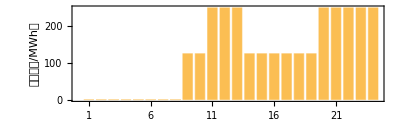

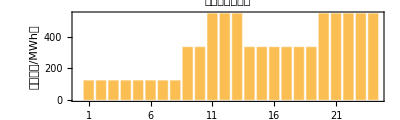

Max generation of Wind power is: 0.974601 p.u.

Annual ultilization hours of Wind power is: 1700.05 h

Max generation of PV is: 1. p.u.

Annual ultilization hours of PV is: 3300.04 h

Solving

Start!

Stage 1:

All time used in optimization by gurobi: 628.8001561RGBColor[1, 0, 0]

Total power generation in a year is:3.14829×10^6 MWh

year ahead dispatch finished! The maximum production of NH3 in a year is: 3.95294×10^8 Nm3 = 300000. t

Total H2 production in a year is: 5.92941×10^8 Nm3, i.e. 52941.2 t

Optimal Capacity of Wind power is: 818.545 MW

Optimal Capacity of Solar power is: 262.965 MW

Optimal Capacity of Alkaline Electrolyzers is: 540. MW

Optimal Capacity of Buffer Tank is: 1.0531×10^6 Nm3, i.e. buffer time is: 9.75094 h

Given Capacity of Battery is: 0. MWh

Total curtailment of wind power in a year is: 131380. MWh. Rate: 0.0417307

Total Power purchase from grid in a year is: 139330. MWh. Rate: 0.0442557

Net Profit of the whole system： 0.0455264 *10^8 ￥

Stage 2:

All time used in optimization by gurobi: 23.993356RGBColor[1, 0, 0]

Optimal Inner electricity price is: 0.2076 ￥/kWh

Optimal Inner hydrogen price is: 1.37361 ￥/Nm3

earning ratio of each agents: {0.0056674,0.00737683,0.00737683}

LOCE of Renewable Energy Generation is: 0.178981 ￥/kWh

LOCH of AEHS is: 1.30297 ￥/Nm3

LOCA of SA is: 3004.02 ￥/t

可再生能源制氢合成氨系统：RGBColor[1, 0, 0]

总投资成本（折算到首年）：7.4773 亿元

运行收益：7.52283 亿元

净收益： 0.0455264 亿元, 收益率：0.00608862

容量费（按最大需量）33 元/kW/月；每月最大网电需量：{247.248,45.8357,38.3648,38.0235,13.015,32.7748,32.3138,35.8884,41.4617,66.2901,91.1942,84.9515} MW；年总容量费：0.253229 亿元

可再生能源发电工段:RGBColor[1, 0, 0]

投资成本（折算到首年）：5.63485 亿元

运行收益：5.66679 亿元

净收益： 0.031935 亿元, 收益率：0.0056674

内部供电价：0.2076 元/度，内部供电量： 30.1691 亿度，内部供电收益： 6.2631 亿元

新能源上网电价：0. 元/度，上网电量：1.3138 亿度，上网收益： 0. 亿元

制氢+储氢工段:RGBColor[1, 0, 0]

投资成本（折算到首年）：1.40653 亿元

运行收益：1.4169 亿元

净收益： 0.0103757 亿元, 收益率：0.00737683

容量费分配系数：0. 对应年总容量费：0. 亿元

制氢内部用电价：0.2076 元/度，制氢内部用电量：28.4913 亿度，内部用电制氢成本： 5.9148 亿元

制氢外购电价：0.35 元/度，制氢外购用电量：1.15572 亿度，外购网电制氢成本： 0.404503 亿元

水价：9. 元/吨，制氢量：52941.2 吨，补水系数： 10 ; 制氢补水费：0.0476471亿元

氢价：1.37361元/标方，氢气年产量：5.92941 亿标方，给合成氨厂供氢收入： 8.14468 亿元

合成氨工段:RGBColor[1, 0, 0]

投资成本（折算到首年）：0.435923 亿元

运行收益：0.439139 亿元

净收益： 0.00321573 亿元, 收益率：0.00737683

容量费分配系数：1. 对应年总容量费：0.253229 亿元

制氨内部用电价：0.2076 元/度，制氨内部用电量：1.67775 亿度，内部用电制氨成本： 0.3483 亿元

制氨外购电价：0.35 元/度，制氨外购用电量：0.237572 亿度，外购网电制氨成本： 0.0831502 亿元

氢价：1.37361元/标方，氢气年产量：5.92941 亿标方，合成氨厂购氢成本： 8.14468 亿元

水价：9. 元/吨，制氨量：300000. 吨，补水系数： 2 ; 制氨补水费：0.054亿元

氨价：3200元/吨，氨气年产量：300000. 吨，出售液氨的收益： 9.6 亿元

电解池超调时间比例：0.260959

发电侧：RGBColor[1, 0, 0]

新能源年总发电量：31.4829 亿度， 其中风电： 27.0123 亿度，光伏发电：4.47054 亿度。年总弃电量： 1.3138 亿度，弃电率： 0.0417307

风电本地消纳：25.6985 亿度(由风电承担弃电任务)；光伏本地消纳：4.47054 亿度。

负荷侧：RGBColor[1, 0, 0]

负荷侧年总用电量：31.5624  亿度，其中新能源供电： 30.1691 亿度，占比： 0.955856; 下网电量：1.3933 亿度，占比： 0.0441442

峰谷平时段上网电量：{0.466531,0.155022,0.692251} 亿度，占全年发电量的比例：{0.0148186,0.004924,0.0219882} 占上网电量的比例：{0.3551,0.117995,0.526906}

峰谷平时段下网电量：{0.478173,0.502198,0.412925} 亿度，占全年发电量的比例：{0.0151884,0.0159514,0.0131159} 占下网电量的比例：{0.343196,0.360439,0.296366}

```mathematica
(*priceFIT is fixed*)
flagCapaIn={{True,True},True,True,{False,False},True};(*{{wind,pv},hydrogen,buffer tank,{battery energy,battery power},print}*)
CapaGivenValIn={800,200,100,0,{0,0}};(*{wind,pv,AE,HS,{ESOCMax, PbatMax}}*)
horizonDispatchIn=365*24*3600;
periodDispatchIn=1*4*900 ;
priceNH3In=3200;
IRRLowerIn=-1;
IRRUpperIn=1;
itrdaysIn=1;
flagGridIn={True,False,False};(*sell,buy,sell-buy; True-constrainted,False-Not constrainted*)
ExchangeRateIn={0.15,0.1,0.2};
ratepAEMinIn=0.0;
LoadNH3MinIn=0.3;
boundarypriceInnerIn=10^3{0.1,0.3};
boundarypriceH2InnerIn={1.,priceNH3In ConstG2L};
nDiscretIn=1000;
rateDiscountIn=0.06;

flagPlaceIn="Xinjiang";(*"Normal","Gansu","Xinjiang"*)
Print["Case Study: ",flagPlaceIn];
periodTOUIn=3600;
flagTOUHIn=False;(*True-priceFIT is time-of-use hourly;Flase-fixed*)
priceFITGValIn=0*0.25*10^3;(*Xinjiang-0.25;Gansu-0.3087;Neimeng-0.2829*)
(*time of use electricity price*)
If[flagPlaceIn=="Xinjiang",
(*Xinjiang*)
pricePeak=0.25*10^3;
priceValley=0*10^3;
priceFlat=0.5*0.25*10^3;
TOUHday=Join[Table[priceValley,{8}],Table[priceFlat,{2}],Table[pricePeak,{3}],Table[priceFlat,{6}],Table[pricePeak,{5}]];
,
pricePeak=0.3087*10^3;
priceValley=0*10^3;
priceFlat=0.5*0.3087*10^3;
TOUHday=Join[Table[priceFlat,{2}],Table[priceValley,{2}],Table[priceFlat,{3}],Table[pricePeak,{2}],Table[priceFlat,{2}],Table[priceValley,{6}],Table[priceFlat,{1}],Table[pricePeak,{6}]];
];
(*TOUHYearIn=Table[TOUHday,{365}]//Flatten;*)
BarChart[TOUHday,Frame->True,FrameLabel->{"时间","电价（元/MWh）"},ChartLabels->(ToExpression[""<>ToString[#]]&/@Range[24]),AspectRatio->0.3]//Print;

flagTOUHPurchIn=False;

pricePurchGVal=0.35*10^3;
If[flagPlaceIn=="Xinjiang",
(*Xinjiang*)
pricePeak=0.5505*10^3;
priceValley=0.1215*10^3;
priceFlat=0.3360*10^3;
TOUHday=Join[Table[priceValley,{8}],Table[priceFlat,{2}],Table[pricePeak,{3}],Table[priceFlat,{6}],Table[pricePeak,{5}]];
,
(*GanSu*)
pricePeak=0.8650*10^3;
priceValley=0.3036*10^3;
priceFlat=0.5843*10^3;
TOUHday=Join[Table[priceFlat,{2}],Table[priceValley,{2}],Table[priceFlat,{3}],Table[pricePeak,{2}],Table[priceFlat,{2}],Table[priceValley,{6}],Table[priceFlat,{1}],Table[pricePeak,{6}]];
];
(*TOUHYearPurchIn=Table[TOUHday,{365}]//Flatten;*)
BarChart[TOUHday,Frame->True,FrameLabel->{"时间","电价（元/MWh）"},PlotLabel->"峰谷平分时电价",ChartLabels->(ToExpression[""<>ToString[#]]&/@Range[24]),AspectRatio->0.3]//Print;

flagOverShootLimitIn=False;(*True-limit the total time of overshoot; False-not limit*)
RateTimeOverShootIn=0.15;
coeffPunishIn=0;
flagMMAIn=True;
ConstCapacityMonthIn=33*10^3/10^4;(*容量费按照最大需量-可优化:W￥/MW/year, or 33￥/kW/month*)
flagConnectedIn=True;(*True-connected to grid; False-off-grid*)
flagBatExistIn=True;(*True-battery; False-No battery*)


tmp=CapaPriceDistributionProgram[flagCapaIn,CapaGivenValIn,horizonDispatchIn,periodDispatchIn,IRRLowerIn,IRRUpperIn,nDiscretIn,boundarypriceInnerIn,boundarypriceH2InnerIn,itrdaysIn,flagGridIn,ExchangeRateIn,periodTOUIn,flagTOUHIn,TOUHYearIn,priceFITGValIn,flagTOUHPurchIn,TOUHYearPurchIn,pricePurchGVal,priceNH3In,ratepAEMinIn,LoadNH3MinIn,rateDiscountIn,flagOverShootLimitIn,RateTimeOverShootIn,coeffPunishIn,flagMMAIn,ConstCapacityMonthIn,flagConnectedIn,flagBatExistIn,flagPlaceIn, WTS,flagWTS,Gridratio,flagGridratio,buffer,flagbuffer];

Print["发电侧：",Red];
Print["新能源年总发电量：",periodDispatchIn/3600ERenFinal/10^5," 亿度， 其中风电： ",periodDispatchIn/3600Total[varsCapaVal[[1]]pwNormMeanValAll]/10^5," 亿度，光伏发电：",periodDispatchIn/3600Total[varsCapaVal[[2]]pvNormMeanValAll]/10^5," 亿度。年总弃电量： ",periodDispatchIn/3600Total[pwCurtDispValAll]/10^5," 亿度，弃电率： ",Total[pwCurtDispValAll]/ERenFinal];
Print["风电本地消纳：",periodDispatchIn/3600Total[varsCapaVal[[1]]pwNormMeanValAll-pwCurtDispValAll]/10^5," 亿度(由风电承担弃电任务)；光伏本地消纳：",periodDispatchIn/3600Total[varsCapaVal[[2]]pvNormMeanValAll]/10^5," 亿度。"];
Print["负荷侧：",Red];
Print["负荷侧年总用电量：",periodDispatchIn/3600Total[pAEDispValAll+pSADispValAll]/10^5" 亿度，其中新能源供电： ",periodDispatchIn/3600(ERenFinal-Total[pwCurtDispValAll])/10^5," 亿度，占比： ",(ERenFinal-Total[pwCurtDispValAll])/Total[pAEDispValAll+pSADispValAll],"; 下网电量：",periodDispatchIn/3600Total[pPurchDispValAll]/10^5," 亿度，占比： ",Total[pPurchDispValAll]/Total[pAEDispValAll+pSADispValAll]];

If[periodDispatchIn==3600,
(*Analysis of Peak-Valley-Flat*)
If[flagPlaceIn=="Normal"||flagPlaceIn=="Gansu",
(*Gansu*)
ListPeak=Join[Range[8,9],Range[19,24]];
ListValley=Join[Range[3,4],Range[12,17]];
temp=Sort[Join[ListPeak,ListValley]];
temp1=Table[{temp[[i]]},{i,1,Length[temp]}];
ListFlat=Delete[Range[1,24],temp1];
,
(*Xinjiang*)
ListPeak=Join[Range[11,13],Range[20,24]];
ListValley=Join[Range[1,8],{}];
temp=Sort[Join[ListPeak,ListValley]];
temp1=Table[{temp[[i]]},{i,1,Length[temp]}];
ListFlat=Delete[Range[1,24],temp1];
];

pwCurtDispPeak=pwCurtDisp[[ListPeak+24#]]&/@Range[0,365-1]//Flatten;
pwCurtDispValley=pwCurtDisp[[ListValley+24#]]&/@Range[0,365-1]//Flatten;
pwCurtDispFlat=pwCurtDisp[[ListFlat+24#]]&/@Range[0,365-1]//Flatten;
pwCurtDispPeakValAll=pwCurtDispPeak/.cRuleStage1;
pwCurtDispValleyValAll=pwCurtDispValley/.cRuleStage1;
pwCurtDispFlatValAll=pwCurtDispFlat/.cRuleStage1;
pPurchDispPeak=pPurchDisp[[ListPeak+24#]]&/@Range[0,365-1]//Flatten;
pPurchDispValley=pPurchDisp[[ListValley+24#]]&/@Range[0,365-1]//Flatten;
pPurchDispFlat=pPurchDisp[[ListFlat+24#]]&/@Range[0,365-1]//Flatten;
pPurchDispPeakValAll=pPurchDispPeak/.cRuleStage1;
pPurchDispValleyValAll=pPurchDispValley/.cRuleStage1;
pPurchDispFlatValAll=pPurchDispFlat/.cRuleStage1;
Print["峰谷平时段上网电量：",periodDispatchIn/3600/10^5{(pwCurtDispPeakValAll//Total),(pwCurtDispValleyValAll//Total),(pwCurtDispFlatValAll//Total)}," 亿度，占全年发电量的比例：",{(pwCurtDispPeakValAll//Total)/ERenFinal,(pwCurtDispValleyValAll//Total)/ERenFinal,(pwCurtDispFlatValAll//Total)/ERenFinal}," 占上网电量的比例：",{(pwCurtDispPeakValAll//Total)/(pwCurtDispValAll//Total),(pwCurtDispValleyValAll//Total)/(pwCurtDispValAll//Total),(pwCurtDispFlatValAll//Total)/(pwCurtDispValAll//Total)}];
Print["峰谷平时段下网电量：",periodDispatchIn/3600/10^5{(pPurchDispPeakValAll//Total),(pPurchDispValleyValAll//Total),(pPurchDispFlatValAll//Total)}," 亿度，占全年发电量的比例：",{(pPurchDispPeakValAll//Total)/ERenFinal,(pPurchDispValleyValAll//Total)/ERenFinal,(pPurchDispFlatValAll//Total)/ERenFinal}," 占下网电量的比例：",{(pPurchDispPeakValAll//Total)/(pPurchDispValAll//Total),(pPurchDispValleyValAll//Total)/(pPurchDispValAll//Total),(pPurchDispFlatValAll//Total)/(pPurchDispValAll//Total)}];
];
```

```mathematica
(*using matlab&gurobi in stage1*)
(*Export matrix of opt problem*)
varsAll=Join[varsDisp,boolsDisp,varsInteger];
varsLen=varsDisp//Length;
boolsLen=boolsDisp//Length;
IntegerLen=varsInteger//Length;
hLen=hFuncDisp//Length;
gLen=gFuncDisp//Length;
aux={varsLen,boolsLen,IntegerLen,hLen,gLen};
Ntemp=10000;
Print[Dynamic["jtr: "<>ToString[jtr]]];
AbsoluteTiming[
hJacob={};
For[jtr=1,jtr<=Floor[hLen/Ntemp],jtr++,
temp=D[hFuncDisp[[Ntemp(jtr-1)+1;;Ntemp jtr]],{varsAll}]//SparseArray;
hJacob=Join[hJacob,temp];
];
If[hLen>Ntemp Floor[hLen/Ntemp],
temp=D[hFuncDisp[[Ntemp Floor[hLen/Ntemp]+1;;hLen]],{varsAll}]//SparseArray;
hJacob=Join[hJacob,temp];
];
]

AbsoluteTiming[
gJacob={};
For[jtr=1,jtr<=Floor[gLen/Ntemp],jtr++,
temp=D[gFuncDisp[[Ntemp(jtr-1)+1;;Ntemp jtr]],{varsAll}]//SparseArray;
gJacob=Join[gJacob,temp];
];
If[gLen>Ntemp Floor[gLen/Ntemp],
temp=D[gFuncDisp[[Ntemp Floor[gLen/Ntemp]+1;;gLen]],{varsAll}]//SparseArray;
gJacob=Join[gJacob,temp];
];
]
fJacob=D[fFuncDispSingle,{varsAll}];
hRhs=-(hFuncDisp/.Dispatch[Thread[varsAll->0]]);
gRhs=-(gFuncDisp/.Dispatch[Thread[varsAll->0]]);
matObj=fJacob;
matCons=Join[hJacob,gJacob];
rhsCons=Join[hRhs,gRhs];
AbsoluteTiming[
Export["auxInfo.mat",aux];
Export["matObj.mat",matObj];
Export["matCons.mat",matCons];
Export["rhsCons.mat",rhsCons//SparseArray];
];
```

```mathematica
(*time of use electricity price*)
(*GanSu*)
pricePeak=0.8650*10^3;
priceValley=0.3036*10^3;
priceFlat=0.5843*10^3;
TOUHday=Join[Table[priceFlat,{2}],Table[priceValley,{2}],Table[priceFlat,{3}],Table[pricePeak,{2}],Table[priceFlat,{2}],Table[priceValley,{6}],Table[priceFlat,{1}],Table[pricePeak,{6}]];
(*Xinjiang*)
pricePurchGVal=0.35*10^3;
pricePeak=0.5505*10^3;
priceValley=0.1215*10^3;
priceFlat=0.3360*10^3;
TOUHday=Join[Table[priceValley,{8}],Table[priceFlat,{2}],Table[pricePeak,{3}],Table[priceFlat,{6}],Table[pricePeak,{5}]];
```

```mathematica
cRuleEPIMin=LinearOptimization[priceInner,{hFunc==0,gFunc\[VectorLessEqual]0},varsDef,Method->"Gurobi"]//Dispatch;
cRuleEPIMax=LinearOptimization[-priceInner,{hFunc==0,gFunc\[VectorLessEqual]0},varsDef,Method->"Gurobi"]//Dispatch;
cRulePH2IMin=LinearOptimization[priceH2Inner,{hFunc==0,gFunc\[VectorLessEqual]0},varsDef,Method->"Gurobi"]//Dispatch;
cRulePH2IMax=LinearOptimization[-priceH2Inner,{hFunc==0,gFunc\[VectorLessEqual]0},varsDef,Method->"Gurobi"]//Dispatch;
Print["Min-Max Value of electricity price is: ",{priceInner/.cRuleEPIMin,priceInner/.cRuleEPIMax}/1000," ￥/kWh"];
Print["Min-Max Value of hydrogen price is: ",{priceH2Inner/.cRulePH2IMin,priceH2Inner/.cRulePH2IMax}," ￥/Nm3"];
```

Min-Max Value of electricity price is: {0.114,0.2858} ￥/kWh

Min-Max Value of hydrogen price is: {1.10818,1.48447} ￥/Nm3

```mathematica
Print["LCOE of Renewable Energy Generation is: ",10InvestRen/(periodDispatchIn/3600 ERenFinal)," ￥/kWh"];
Print["LCOH of AEHS is: ",(10^4InvestAEHS+10^8(CostH2Inner+CostH2Purch))/(periodDispatchIn/3600 Total[qH2InDispValAll])," ￥/Nm3"];
Print["LCOA of SA is: ",10^4(InvestSA+10^4(CostNH3Inner+CostNH3Purch+costH2))/mNH3Max," ￥/t"];
```

LOCE of Renewable Energy Generation is: 0.183016 ￥/kWh

LOCH of AEHS is: 1.40677 ￥/Nm3

LOCA of SA is: 3161.01 ￥/t